```mathematica
(*Coefficients after local sqrt(X) on L={k1,...,km}-uniform X-stabilized Hypergraph state*)
koeffX[L_,NN_]:=Table[1/(2 √2)^NN Sum[ Sum[Binomial[NN-e,w-m]*Binomial[e,m]((1+I)^NN(-I)^(w+e-2m))(-1)^(Sum[Binomial[w,L[[ii]]],{ii,1,Length[L]}]),{m,0,e}],{w,0,NN}],{e,0,NN}];
(*Coefficients after local sqrt(Y) on L={k1,...,km}-uniform Y-stabilized Hypergraph state*)
koeffY[L_,NN_]:=
Table[(1+I)^NN/(2 √2)^NN Sum[ Sum[Binomial[NN-e,w-m]*Binomial[e,m](-1)^(Sum[Binomial[w,L[[ii]]],{ii,1,Length[L]}] +w)(-1)^m,{m,0,e}],{w,0,NN}],{e,0,NN}];
(* Overlap of sqrt(X)-transformed state with cos(theta)|0>+e^(iphi)sin(theta)|1> *)
gX[k_,NN_]:=Sum[Binomial[NN,w] aa^w(√(1-aa^2))^(NN-w)*Abs[koeffX[{k},NN][[w+1]]],{w,0,NN}];
(* Overlap of Y-transformed state with cos(theta)|0>+e^(iphi)sin(theta)|1> *)
gYi[k_,NN_]:=Sum[Binomial[NN,w]aa^w(√(1-aa^2))^(NN-w)ⅇ^(I*bb*(NN-w))*koeffY[{k},NN][[w+1]],{w,0,NN}];
```

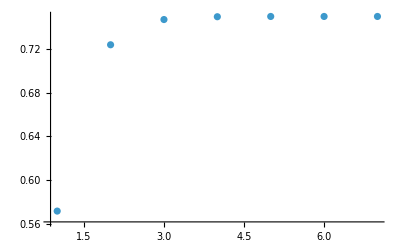

```mathematica
(* Numerical computation of GEM for Y-stabilized 4j-qubit 3-uniform Hypergraph states*)
jmin = 1;
jmax = 7;
ListPlot[Table[1-NMaximize[{Abs[gYi[3,4jjj]]^2,{0<=aa<=1,0<=bb<=π}},{aa,bb}][[1]],{jjj,jmin,jmax}],PlotRange->All]
```

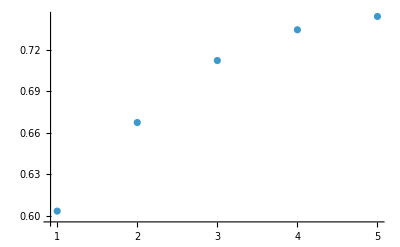

```mathematica
(* Numerical computation of GEM for Y-stabilized 8j-qubit 5-uniform Hypergraph states*)
jmin = 1;
jmax = 5;
ListPlot[Table[1-NMaximize[{Abs[gYi[5,8jjj]]^2,{0<=aa<=1,0<=bb<=π}},{aa,bb}][[1]],{jjj,jmin,jmax}],PlotRange->All]
```

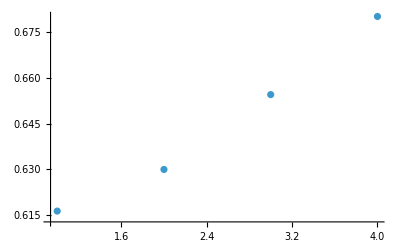

```mathematica
(* Numerical computation of GEM for Y-stabilized 16j-qubit 9-uniform Hypergraph states*)
jmin = 1;
jmax = 4;
ListPlot[Table[1-NMaximize[{Abs[gYi[9,16jjj]]^2,{0<=aa<=1,0<=bb<=π}},{aa,bb}][[1]],{jjj,jmin,jmax}],PlotRange->All]
```